```mathematica
coefs={-0.1628144585364618,1.0938240550863623,-1.7893*^-12,-0.0388330290615209,4.2068*^-12,0.0058637635731647,-3.8354*^-12,-0.0012449499435649,1.3109*^-12,0.0003035681797625,1.9562*^-12,-0.0000795509260935,-8.6277*^-12,0.0000218142857332,9.5162*^-12,-6.1819173587*^-6,6.307*^-13,1.7974479634*^-6,-1.43203*^-11,-5.334745204*^-7,1.42301*^-11,1.609769975*^-7,-4.9777*^-12,-4.92412545*^-8,-2.09951*^-11,1.52481128*^-8,2.77066*^-11,-4.7711989*^-9,-1.13903*^-11,1.4635423*^-9,-1.13087*^-11,-3.706093*^-10};
```

```mathematica
F[x_]:=Sin[x]
min=-2Pi;
max=2Pi;
```

```mathematica
FourierApprox[coefs_][x_]:=Sum[coefs[[i+1]]*Sin[i*x], {i, 0,Length[coefs]-1}]
TaylorApprox[coefs_][x_]:=Sum[coefs[[i+1]]*x^i/Factorial[i], {i, 0, Length[coefs]-1}]
IntegralLoss[f_]:=NIntegrate[(F[x]-f[f[x]])^2, {x, min, max}]
```

```mathematica
approx=FourierApprox[coefs];
```

```mathematica
IntegralLoss[approx]
```

1.36716×10^-19

```mathematica
Iconize[approx[x]]
```

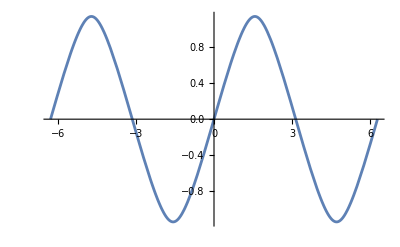

```mathematica
Plot[ approx[x], {x, min, max}]
```

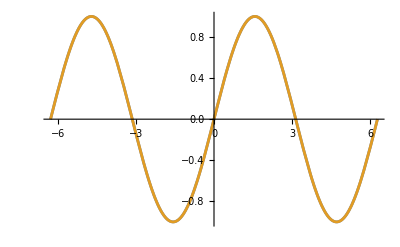

```mathematica
Plot[{F[x], approx[approx[x]]}, {x, min, max}]
```

```mathematica
approx[x]
```

0.+1.09382 Sin[x]-1.7893×10^-12 Sin[2 x]-0.038833 Sin[3 x]+4.2068×10^-12 Sin[4 x]+0.00586376 Sin[5 x]-3.8354×10^-12 Sin[6 x]-0.00124495 Sin[7 x]+1.3109×10^-12 Sin[8 x]+0.000303568 Sin[9 x]+1.9562×10^-12 Sin[10 x]-0.0000795509 Sin[11 x]-8.6277×10^-12 Sin[12 x]+0.0000218143 Sin[13 x]+9.5162×10^-12 Sin[14 x]-6.18192×10^-6 Sin[15 x]+6.307×10^-13 Sin[16 x]+1.79745×10^-6 Sin[17 x]-1.43203×10^-11 Sin[18 x]-5.33475×10^-7 Sin[19 x]+1.42301×10^-11 Sin[20 x]+1.60977×10^-7 Sin[21 x]-4.9777×10^-12 Sin[22 x]-4.92413×10^-8 Sin[23 x]-2.09951×10^-11 Sin[24 x]+1.52481×10^-8 Sin[25 x]+2.77066×10^-11 Sin[26 x]-4.7712×10^-9 Sin[27 x]-1.13903×10^-11 Sin[28 x]+1.46354×10^-9 Sin[29 x]-1.13087×10^-11 Sin[30 x]-3.70609×10^-10 Sin[31 x]

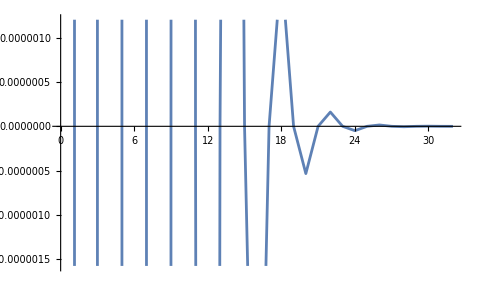

```mathematica
ListLinePlot[coefs]
```

## Bulk

```mathematica
min=-1;max=1;
```

```mathematica
type=TaylorApprox;
cl={{0.6544938334242058, -0.0002342440818652, 1.7236010419120558, 0.0109611200495767, -2.2848301905761610, -0.2500066265281824, -0.7951573347703617, -1.3266113060423981, 0.0013102973686905, -0.0000496057501528, 0.0002969838294944, -0.0006906056051093, 0.0001127109579040, -0.0005539060719803, 0.0004752701166141, 0.0000849763168174}, {1.2133526737926259, 1.3773051433058070, 0.2415090153008883, 0.1414370318353121, -1.8120416605253313, 2.8591972191636756, -0.9522523063285991, -0.6394980874288446, -0.0146111700950444, -0.0082029767114486, -0.0078841298293077, -0.0002166021614984, 0.0052620568516678, -0.0016254891483315, -0.0005393749757924, -0.0004428352569853}, {0.6681212059096210,0.7375810103070287,-0.2067721684958095,-1.5955910620428442,-6.0844379470505201,0.7862176817334150,3.4802373508118647,0.1645506881444374,-0.1006597425189200,0.0389826714189264,0.1011808328694398,-0.0905902823022869,-0.0245818760611512,-0.0385559662942524,-0.0336429263629433,0.0128402038731899}, {0.4988532491017690,0.8780691307977085,0.4871607306282898,0.1261744529474822,0.0991019940960358,0.1808920736062259,-0.6953921353605117,-1.4144360565320198,-0.0011774025366700,-0.0003075065600903,-0.0002272573984056,0.0005807352974941,-0.0000327288413811,0.0004350924806446,0.0015148317952284,0.0006971222239573},
{0.4067541658187361,0.7495902703454348,-0.2404351670551470,0.1751210938600332,-0.0847208007411097,0.0402503898627490,0.4677396118108469,1.1438344531591413,0.0008346646404910,0.0007823297641539,0.0021333623352009,0.0011276904556247,-0.0010853992053448,-0.0010784355641071,-0.0002858873816509,0.0003282922233928},
{1.0910983620580981,0.2914449406596135,0.3018109326251505,-3.7380596977944918,-6.6779969800081433,4.3039708562674077,-2.1835959464916428,-1.9778093059218158,0.0337956988836869,0.0282835779731927,-0.1135100553245500,0.0059732043491849,-0.0592361062010815,0.0462989016675580,-0.0086739024851439,0.0513735429567559}};
fl={#^2+1&, 2*3#&, Cos, Exp, Log[#+2]&, If[#<0, #+1, #^2]&};
```

```mathematica
ll=Table[F[x_]:=fl[[i]][x]; IntegralLoss[type[cl[[i]]]], {i, Length[cl]}];
Grid[Transpose[{ll, fl}]]
```

0.0000422338 | #1^2+1&
28.6678 | 2 3 #1&
0.0186533 | Cos
1.78436×10^-7 | Exp
5.3584×10^-7 | Log[#1+2]&
0.070538 | If[#1<0,#1+1,#1^2]&

## Bulk

```mathematica
min=-1;max=1;
```

```mathematica
type=FourierApprox;
cl={{1.2246956445138337,1.2166975111433873,0.0729657800279132,-0.8484101363295267,-0.1202852538834846,0.3358314305318161,0.1280581510291586,-0.2705251427656272,-0.1042962853715252,0.1216967356850766,0.0651423388719563,-0.0318554121278124,-0.0299608383967803,0.0162692309806894,0.0098589392920010,0.0079168253633748},
{-1.1156337084397527,-4.1882907264159606,1.3463625637052303,1.1521040253985171,-0.6387964432119824,-0.6447094270304321,0.3568482140999845,0.3700252737977887,-0.2311118313252239,-0.2173404823671478,0.1138653202439857,0.1157808212608941,-0.0412714256850812,-0.0680433112097345,0.0056845303836164,0.0356157615538107},
{0.4589564375149398,1.3405600868264866,0.0161843843348401,-0.0995243347447972,-0.0560107439552761,0.2130315511022402,0.1110016445669023,-0.1589402720224176,-0.0417847298125124,-0.0056767731374791,0.0202464316735820,-0.0118358216768222,-0.0652179506358034,0.0318657944914093,0.0197029790477391,0.0158822621725416},
{-1.3806748980463894,0.8256176487151617,0.7745770978034802,-0.5887295166935065,-0.2487646925309642,0.4281944211194647,0.2630144725443348,-0.4211744176589940,-0.1152093200899925,0.2437154511010796,0.0639784501560614,-0.1711056437656425,-0.0158415953018809,0.0587492800411200,-0.0018060194612293,-0.0287431977360369},
{-0.2336442962043032,0.4438788063612152,0.6917248932268039,-0.0527781328594555,-0.2492689620287993,0.0255992805054442,0.0856836365031309,0.0009507448685938,-0.0186721059082200,0.0026705214269635,-0.0102300151428505,0.0032228529311020,0.0121886702872176,-0.0024079783698715,-0.0047379545805702,0.0003040585426881},
{1.2768455876503177,1.1863084861971538,-0.5565398628597755,-0.7052035374514035,-0.1123114095533313,0.2446146729420072,-0.2363743551935658,-0.1836986512945765,0.0204443759936088,0.1002962394110359,-0.1083950333131216,-0.0996355700141206,0.0076166479422958,0.0394593509131775,-0.0385854877085064,-0.0304829829755257}};
fl={#^2+1&, 2*3#&, Cos, Exp, Log[#+2]&, If[#<0, #+1, #^2]&};
```

```mathematica
ll=Table[F[x_]:=fl[[i]][x]; IntegralLoss[type[cl[[i]]]], {i, Length[cl]}];
Grid[Transpose[{ll, fl}]]
```

3.74991 | #1^2+1&
12.6413 | 2 3 #1&
2.23477 | Cos
2.85159 | Exp
1.16718 | Log[#1+2]&
1.41415 | If[#1<0,#1+1,#1^2]&